```mathematica
i = -Graphics-
```

-Graphics-

```mathematica
corners = ImageCorners[i,3,.01,5]
```

{{237.5,152.5},{260.5,79.5},{225.5,151.5},{241.5,79.5},{227.5,78.5},{219.5,78.5},{79.5,74.5},{217.5,150.5},{205.5,78.5},{77.5,144.5},{100.5,75.5},{203.5,150.5},{257.5,152.5},{93.5,75.5},{50.5,74.5},{114.5,75.5},{98.5,145.5},{48.5,143.5},{91.5,145.5},{156.5,76.5},{139.5,147.5},{111.5,146.5},{141.5,76.5},{153.5,148.5}}

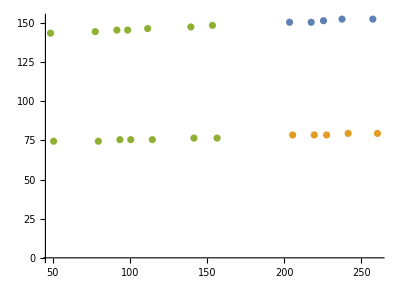

```mathematica
ListPlot[FindClusters[corners],AspectRatio->Automatic]
```

```mathematica
For[x=1,x<Length[corners]+1,++x,Print[corners[[x]]]]
```

{237.5,152.5}

{260.5,79.5}

{225.5,151.5}

{241.5,79.5}

{227.5,78.5}

{219.5,78.5}

{79.5,74.5}

{217.5,150.5}

{205.5,78.5}

{77.5,144.5}

{100.5,75.5}

{203.5,150.5}

{257.5,152.5}

{93.5,75.5}

{50.5,74.5}

{114.5,75.5}

{98.5,145.5}

{48.5,143.5}

{91.5,145.5}

{156.5,76.5}

{139.5,147.5}

{111.5,146.5}

{141.5,76.5}

{153.5,148.5}

```mathematica
corners[[1]]
```

{237.5,152.5}

```mathematica
Max[corners]
```

```mathematica
corners[[;;,2]]
```

{152.5,79.5,151.5,79.5,78.5,78.5,74.5,150.5,78.5,144.5,75.5,150.5,152.5,75.5,74.5,75.5,145.5,143.5,145.5,76.5,147.5,146.5,76.5,148.5}

```mathematica
minX = Min[corners[[;;,1]]]
```

48.5

```mathematica
minY = Min[corners[[;;,2]]]
```

74.5

```mathematica
maxX = Max[corners[[;;,1]]]
```

260.5

```mathematica
maxY = Max[corners[[;;,2]]]
```

152.5

```mathematica
z = ImageTrim[i,{{minX,minY},{maxX,maxY}}]
```

-Graphics-

```mathematica
imageData = ImagePartition[z,Scaled[{1/10,1}]][[1,;;]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
whiteTest = ImageMeasurements[ imageData[[1]],"Mean"]
```

{0.908993,0.866728,0.820248}

```mathematica
blackTest = ImageMeasurements[ imageData[[2]],"Mean"]
```

{0.578135,0.555723,0.526566}

Sum::argmu: Sum called with 1 argument; 2 or more arguments are expected.

```mathematica
Total[blackTest]
```

1.66042

```mathematica
Total[whiteTest]
```

2.59597

```mathematica
Total[ImageMeasurements[ imageData[[1,2]],"Mean"]]
```

1.66042

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
classifyBar[x_]:= If[x < 1.75,1,0]
classifyBar[0.49]
```

1

```mathematica
quantifyBar[x_] := Total[ImageMeasurements[x,"Mean"]]
```

```mathematica
For[x=1,x<Length[imageData]+1,x++,Print[{classifyBar[quantifyBar[imageData[[x]]]],quantifyBar[imageData[[x]]]}]]
```

{0,2.59597}

{1,1.66042}

{1,1.54379}

{0,2.12715}

{1,1.27265}

{0,1.75938}

{0,1.8915}

{1,1.4285}

{1,1.57755}

{0,2.49864}